Introduction

Mathematica is a symbolic algebra system.  It is capable of performing numerical and symbolic calculations.

To enter calculations place your cursor between two cells.  It will change orientation from vertical to horizontal.

Try making a new cell to add 23 and 56.  Put your cursor between this cell and the next one.  With the cursor oriented horizontally, type 23 + 56.  Then hold the shift key and press enter.  You should see the sum output as 79.  Pressing shift and enter together tells Mathematica to evaluate the expression.

Mathematica knows pretty much every function  you can think of.  All functions and commands start with a capital letter.  For example to evaluate sin(π/3), type Sin[Pi/3] in a new cell.  Note the capital letters in Sin and Pi and the square brackets around the argument.  Mathematica uses square brackets to enclose arguments of functions or commands.  You can use parentheses to group expressions as you would if you wrote them out.  Try putting your cursor in the cell below and pressing shift-enter.

```mathematica
Expand[(x + 2)(x - 3)]
```

-6-x+x^2

You can define functions in Mathematica.  For example, shift enter in the cell below.

```mathematica
f[x_]:= x^2 + 3x + 2
```

Note the underscore after the x.  The underscore indicates that x is a variable.  You can evaluate f at x = 5 by typing f[5] in a new cell and pressing shift enter.

```mathematica
f[5]
```

42

Sheep Problem, Section 1.2 #1

In this course, we will do a lot of work with data  so you will need to understand how Mathematica works with lists and matrices.  This provides an overview and some examples, for more complete information click on Help above and search on list or matrix.  A list in Mathematica is enclosed in set bracketrs {}.  Ordered pairs can be entered as a list of length two lists.  This forms an n by 2 matrix.  If you shift enter on the command below, you will enter the sheep data from problem 1, Section 1.2 of the text.

```mathematica
data:={{1814,125},{1824,275},{1834,830},{1844,1200},{1854,1750},{1864,1650}}
```

You can see the data written as ordered pairs by using the command

```mathematica
MatrixForm[data]
```

(1814 | 125
1824 | 275
1834 | 830
1844 | 1200
1854 | 1750
1864 | 1650)

Once the data is entered, you can refer to particular entries in the list or matrix.  For example, data[[1,2]] is the row 1, column 2 entry in the data matrix.  (Try it.)  What would you type to get the entry equal to 1750?  The Table command enables you to generate a table of values.

```mathematica
data[[1,2]]
```

125

Usually, we change the year so that the first year is year 0.  The command will establish 1814 as year 0.

```mathematica
normeddata := Table[{data[[i,1]]-1814,data[[i,2]]},{i,1,6}]
```

```mathematica
MatrixForm[normeddata]
```

(0 | 125
10 | 275
20 | 830
30 | 1200
40 | 1750
50 | 1650)

You can have Mathematica plot the data by using the ListPlot command.

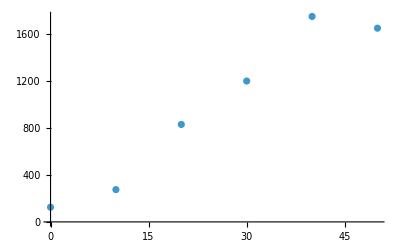

```mathematica
Graph1 = ListPlot[normeddata]
```

You can make the points larger by adding the command PlotStyle→ AbsolutePointSize[Large]

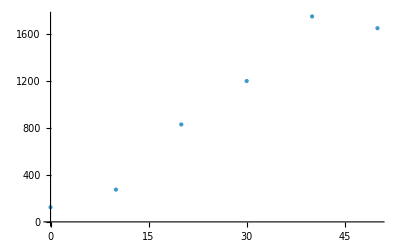

```mathematica
BigPoints = ListPlot[normeddata,PlotStyle-> AbsolutePointSize[Large]]
```

The command below will connect the data points with straight lines.

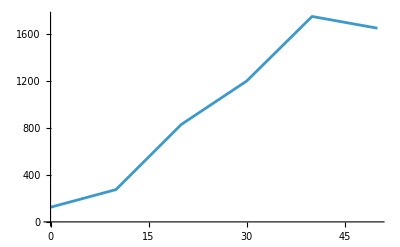

```mathematica
connected=ListPlot[normeddata,Joined->True]
```

If you want both large points and connected, show both graphs above at the same time.

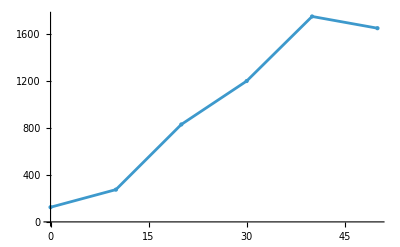

```mathematica
Show[BigPoints,connected]
```

What does data set change (as defined below) represent?  Shift enter in that cell to enter the data.

```mathematica
change:=Table[{normeddata[[i+1,1]],normeddata[[i+1,2]]-normeddata[[i,2]]},{i,1,5}]
```

The next three commands generate plots like those above for change.  Since they are all in the same cell (note the bracket on the right), putting your cursor anywhere in the cell and hitting shift enter, will execute all three command.  If you don’t want to see the output of the first two commands and just want to see the final graph, put a semicolon at the end of each of the first two commands.  the semicolon suppresses the output.

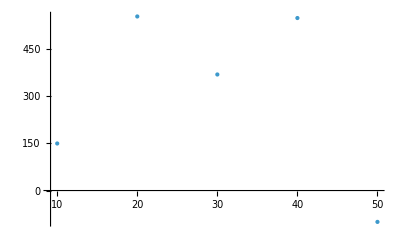

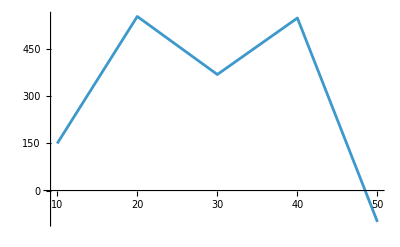

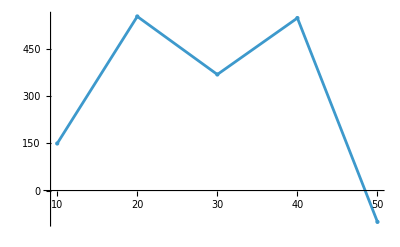

```mathematica
BigPoints2 = ListPlot[change, PlotStyle-> AbsolutePointSize[Large]]
connected2=ListPlot[change,Joined->True]
Show[BigPoints2, connected2]
```

What does the data set below represent?

```mathematica
popvschange:={{data[[1,2]], change[[1, 2]]},{data[[2,2]], change[[2,2]]},{data[[3,2]],change[[3,2]]}, {data[[4,2]], change[[4,2]]}, {data[[5,2]],change[[5,2]]}}
```

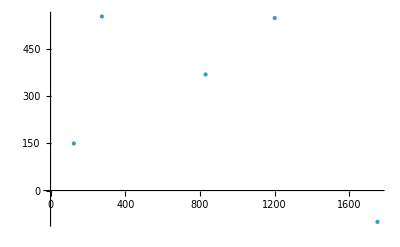

```mathematica
BigPoints3 = ListPlot[popvschange, PlotStyle-> AbsolutePointSize[Large]]
```

We can use the Fit command to fit a line to a data set.  The command Fit[popvschange, {x,1},x] will fit a line to the popvschange data. The {x,1} part of the command is a basis for the vector space of all lines, so this command fits the best line to the data using the least squares fit criterium.

```mathematica
fitline = Fit[popvschange, {x, 1}, x]
```

450.597-0.174158 x

The command below fits a line through the origin to popvschange.  Note that the basis is just x, so we are only considering lines of the form y = mx.  Why would we want to force the line to go through the origin?  What model are we checking when we do this?

```mathematica
originline = Fit[popvschange,{x},x]
```

0.182385 x

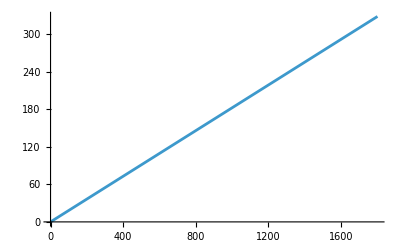

```mathematica
plotline = Plot[originline, {x,0,1800}]
```

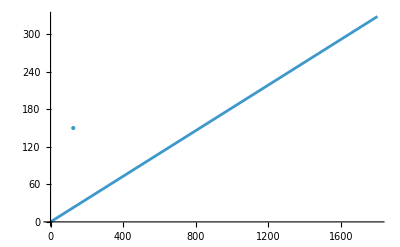

```mathematica
Show[plotline,BigPoints3]
```

How come there’s only one data point?  The vertical axis only goes from 0 to 400, but many of the changes are above 400.  The command below uses the PlotRange command to force the vertical axis to range from -200 to 600.

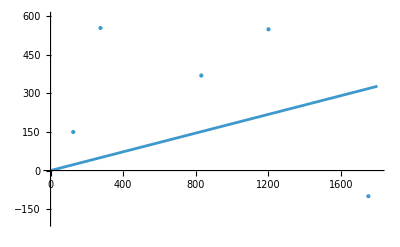

```mathematica
Show[plotline,BigPoints3,PlotRange->{-200, 600}]
```

This doesn’t look good, but let’s forge on.  The Do loop below uses the best fit line through the origin to model the data set.

```mathematica
p[0] = 125
Do[p[n]=1.182385p[n-1], {n,1,5}]
```

125

```mathematica
Table[p[n],{n,0,5}]
```

{125,147.798,174.754,206.627,244.312,288.871}

```mathematica
MatrixForm[%]
```

(125
147.798
174.754
206.627
244.312
288.871)

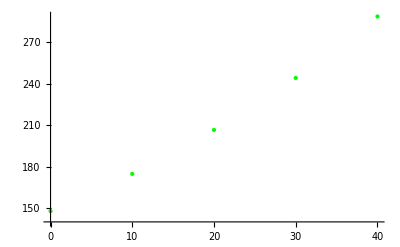

```mathematica
BigPoints4 =ListPlot[Table[{normeddata[[i,1]],p[i]},{i,1,6}], PlotStyle-> {AbsolutePointSize[Large], Green}]
```

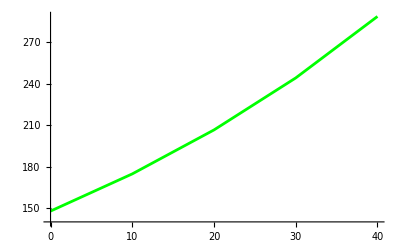

```mathematica
joined = ListPlot[Table[{normeddata[[i,1]],p[i]},{i,1,6}],Joined ->True, PlotStyle->Green]
```

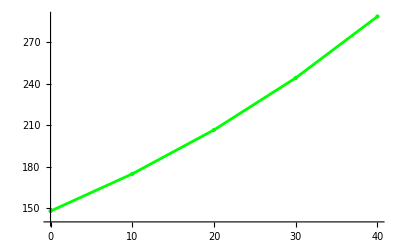

```mathematica
Show[BigPoints4, joined]
```

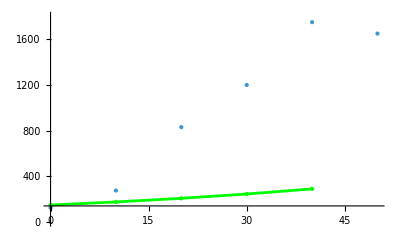

```mathematica
Show[BigPoints4,joined,BigPoints, PlotRange->{0,1800}]
```

Uh, this didn’t work.  Why would I say that?  Let’s try another model.

The data set below assumes a carrying capacity of 1600.

```mathematica
ccmodelvschange:={{data[[1,2]](1600-data[[1,2]]),change[[1,2]]}, {data[[2,2]](1600-data[[2,2]]),change[[2,2]]}, {data[[3,2]](1600-data[[3,2]]),change[[3,2]]}, 
{data[[4,2]](1600-data[[4,2]]),change[[4,2]]}, 
{data[[5,2]](1600-data[[5,2]]),change[[5,2]]}}
```

Make sure you understand what the plot below represents.

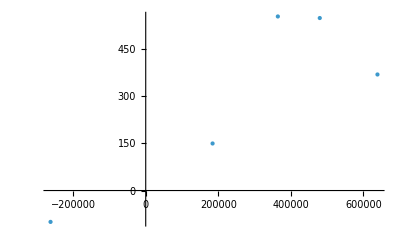

```mathematica
ListPlot[ccmodelvschange,PlotStyle-> AbsolutePointSize[Large]]
```

```mathematica
MatrixForm[ccmodelvschange]
```

(184375 | 150
364375 | 555
639100 | 370
480000 | 550
-262500 | -100)

Make sure you know what the command below does.

```mathematica
Fit[ccmodelvschange,{x},x]
```

0.000865164 x

```mathematica
pcc[0] = 125
Do[pcc[n]=pcc[n-1]+.000865(1600 - pcc[n-1])pcc[n-1], {n,1,6}]
```

125

```mathematica
Table[pcc[n],{n,0,6}]
```

{125,284.484,608.205,1129.99,1589.4,1603.97,1598.46}

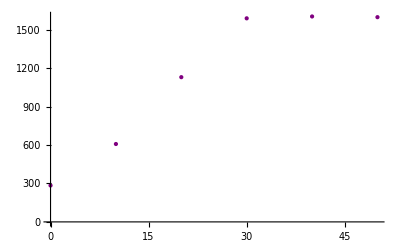

```mathematica
pccBigPoints = ListPlot[Table[{normeddata[[i,1]],pcc[i]},{i,1,6}],PlotStyle-> {AbsolutePointSize[Large], Purple}]
```

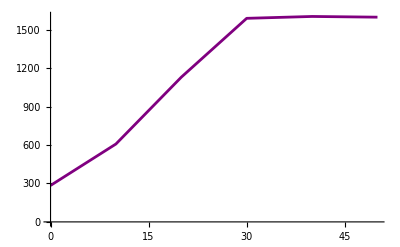

```mathematica
pccJoined =  ListPlot[Table[{normeddata[[i,1]],pcc[i]},{i,1,6}],PlotStyle-> {Purple},Joined->True]
```

What does the graph below tell us?

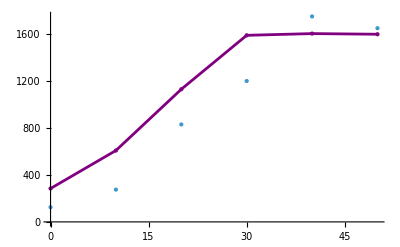

```mathematica
Show[pccBigPoints, BigPoints, pccJoined, PlotRange->{0, 1750}]
```

Perform a similar analysis on the United States population data given in problem 2, p. 16.  The data for problem 2 is given below.

```mathematica
USdata:={{1790,3929},{1800,5308},{1810,7240},{1820,9638},{1830,12866},{1840,17069},{1850,23192},{1860,31443},{1870,38558},{1880,50156},{1890,62948},{1900,75995},{1910,91972},{1920,105711},{1930,122755},{1940,131669},{1950,150697},{1960,179323},{1970,203212},{1980,226505},{1990,248710},{2000,281416}}
```

See Data written as ordered pairs

```mathematica
MatrixForm[USdata]
```

(1790 | 3929
1800 | 5308
1810 | 7240
1820 | 9638
1830 | 12866
1840 | 17069
1850 | 23192
1860 | 31443
1870 | 38558
1880 | 50156
1890 | 62948
1900 | 75995
1910 | 91972
1920 | 105711
1930 | 122755
1940 | 131669
1950 | 150697
1960 | 179323
1970 | 203212
1980 | 226505
1990 | 248710
2000 | 281416)

Get a point from the data (ew its not 0 indexed)

```mathematica
USdata[[1, 2]]
```

3929

Normalize the data such that the year is given by the number of years after 1790

```mathematica
USNormedData := Table[ {USdata[[i, 1]]-1790, USdata[[i, 2]]}, {i, 1, 22}]
MatrixForm[USNormedData]
```

(0 | 3929
10 | 5308
20 | 7240
30 | 9638
40 | 12866
50 | 17069
60 | 23192
70 | 31443
80 | 38558
90 | 50156
100 | 62948
110 | 75995
120 | 91972
130 | 105711
140 | 122755
150 | 131669
160 | 150697
170 | 179323
180 | 203212
190 | 226505
200 | 248710
210 | 281416)

Plot the normalized US data

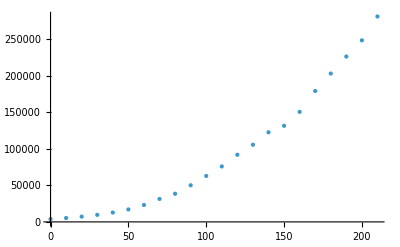

```mathematica
USPoints = ListPlot[USNormedData, PlotStyle->AbsolutePointSize[Large]]
```

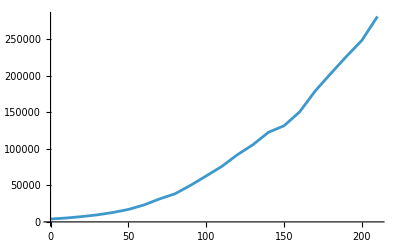

```mathematica
USConnected  = ListPlot[USNormedData, Joined->True]
```

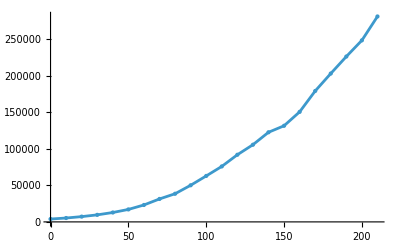

```mathematica
Show[USPoints, USConnected]
```

Plot the changes between the points in the graph

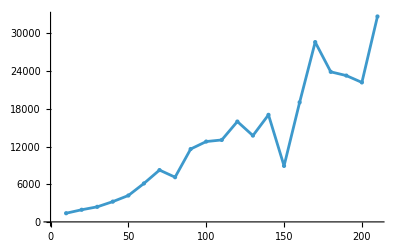

```mathematica
USChange := Table[{USNormedData[[i+ 1, 1]], USNormedData[[i + 1, 2]]-USNormedData[[i, 2]]}, {i, 1, 21}]
USChangePoints := ListPlot[USChange, PlotStyle->AbsolutePointSize[Large]]
USChangeConnected := ListPlot[USChange, Joined->True]
Show[USChangePoints, USChangeConnected]
```

Plot a line of best fit for the change plot .

```mathematica
USFitLine = Fit[USChange, {x, 1}, x]
```

-1907.52+137.465 x

Plot a line of best fit through the origin

```mathematica
USOriginLine = Fit[USChange, {x}, x]
```

124.157 x

Plot the lines of best fit against the USChange data

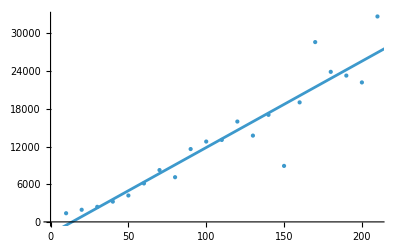

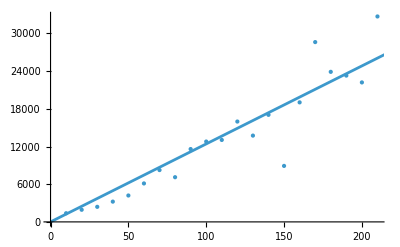

```mathematica
USPlotLine := Plot[USFitLine, {x, 0, 1800}]
Show[USChangePoints, USPlotLine]
USOriginPlot := Plot[USOriginLine, {x, 0, 1800}]
Show[USChangePoints, USOriginPlot]
```

The plot of the change in the data-points approximates a linear relationship, ΔPopulation = k * number of years after 1790 for some real number k

k = 124.157, which is the slope of the line through the origin

Let P(x) be the function that represents the US population x years after 1790. P(x) = P(x - 1) + 124.157x

```mathematica
p[0] = 3929
Do[p[n]=p[n-1]+124.157*USNormedData[[n, 1]], {n, 1, 21}]
Table[p[n], {n, 0, 21}]
```

3929

{3929,3929.,5170.57,7653.71,11378.4,16344.7,22552.5,30002.,38693.,48625.5,59799.6,72215.3,85872.6,100771.,116912.,134294.,152917.,172783.,193889.,216237.,239827.,264659.}

```mathematica
MatrixForm[%]
```

(3929
3929.
5170.57
7653.71
11378.4
16344.7
22552.5
30002.
38693.
48625.5
59799.6
72215.3
85872.6
100771.
116912.
134294.
152917.
172783.
193889.
216237.
239827.
264659.)

Plot the predicted data against the actual data

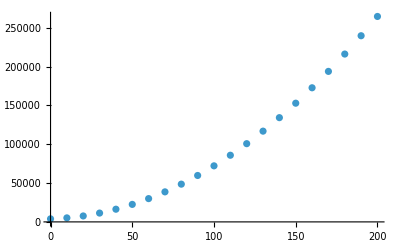

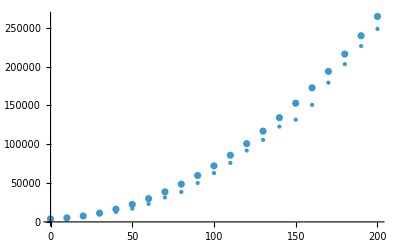

```mathematica
USPredictedData = ListPlot[Table[{USNormedData[[i, 1]], p[i]}, {i, 1, 22}]]
Show[USPredictedData, USPoints]
```

Is this good? Do I get credit for this? Idk I was trying to install mathematica while you were explaining what the assignment was ;-;